```mathematica
MHz=10^6;μs=10^-6;
```

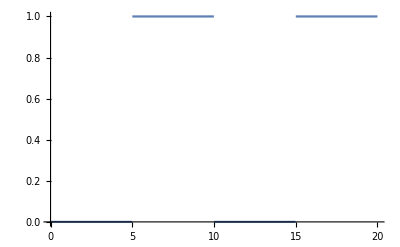

```mathematica
Plot[(1-SquareWave[{0,1},.1t]),{t,0,20},PlotRange->All]
```

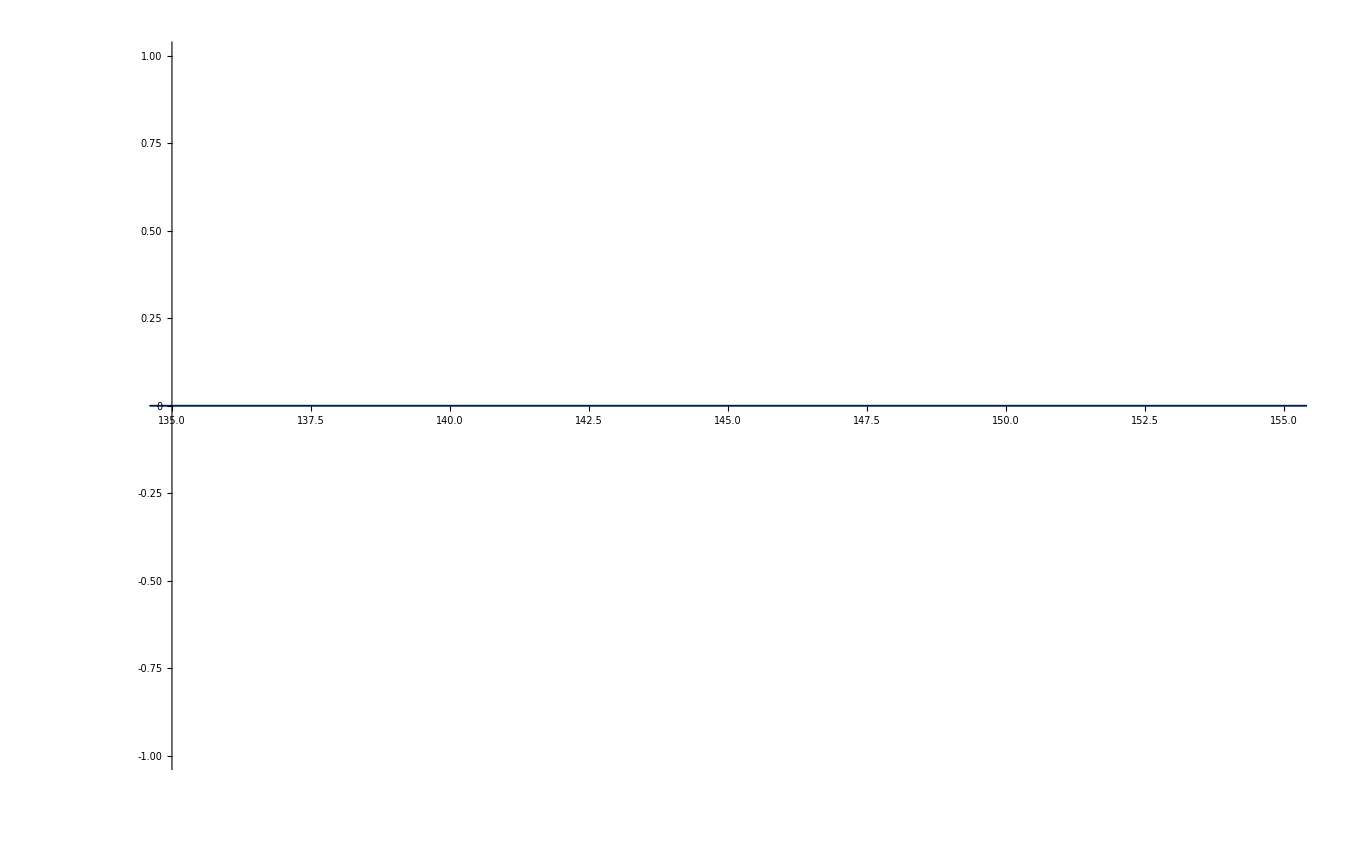

```mathematica
ClearAll["Global`*"]
sampleRate=500;duration=1;dt=1/sampleRate;
data=ParallelTable[SquareWave[{0,1},.1t]Sin[2Pi 145 t](1-SquareWave[{0,1},.1t])Sin[2Pi 140 t],{t,0,duration,dt}];
fdata=Abs[Fourier[data]];
Periodogram[data,10000,SampleRate->sampleRate,ScalingFunctions->"Linear",PlotRange->{{135,155},{0,All}}]
```

```mathematica
Max[fdata]
```

15.8063

```mathematica
dt
```

1/1000

```mathematica
Integrate[Exp[-4 χ^2],{χ,-∞,x}]
max=1/4 √π (1+Erf[2 ∞])//N;
```

1/4 √π (1+Erf[2 x])

```mathematica
FindRoot[0.1 max==1/4 √π (1+Erf[2 x]),{x,-.5}]
FindRoot[0.9max==1/4 √π (1+Erf[2 x]),{x,0.5}]
```

{x→-0.453097}

{x→0.453097}

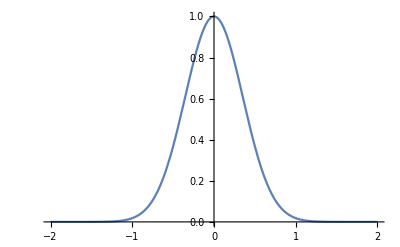

```mathematica
Plot[Exp[-4 χ^2],{χ,-2,2}]
```

```mathematica
1/4 √π (1+Erf[2 ∞])//N
```

0.886227

```mathematica
0.4530969012184116*2
```

0.906194

```mathematica
0.62/2 max
```

0.27473

```mathematica
Exp[-4 χ^2]/.χ->0.27473
```

0.739407

```mathematica
-π^2/8 (140 MHz)^2((3mm)/(4.26(mm MHz)))^2
```

-11991.9

```mathematica
3mm
```

```mathematica
τ=(3mm)/(4.26(mm MHz))
```

7.04225×10^-7

```mathematica
(0.64 10^3)/4.26
```

150.235

```mathematica
Exp[-6.8 10^-2 3^2 140^2]
```

General::munfl: Exp[-11995.2] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
FourierSeries[SquareWave[{-1,1},x],x,2]//FullSimplify//N
```

-0.0188801 (0.877583-3.80403 Cos[x]) Sin[x]

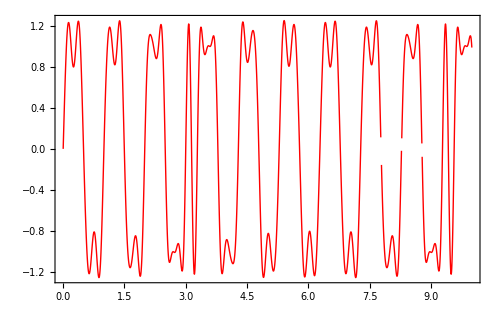

```mathematica
Plot[Evaluate[FourierSeries[SquareWave[{-1,1},x],x,30]//N],{x,0,10}]
```

```mathematica
?FourierSinSeries
```

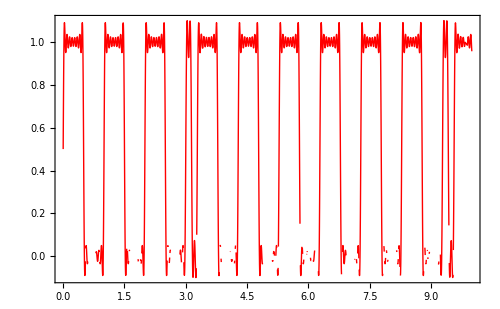

```mathematica
Plot[Evaluate[FourierSeries[SquareWave[{0,1},x],x,100]],{x,0,10}]
```

```mathematica
FunctionExpand[HannWindow[x]]
```

Piecewise[{{1/2+1/2 Cos[2 π x], -1/2≤x≤1/2}, {0, True}}]

```mathematica
Piecewise[{{1/2+1/2 Cos[2 π x], -1/2≤x≤1/2}, {0, True}}]
```

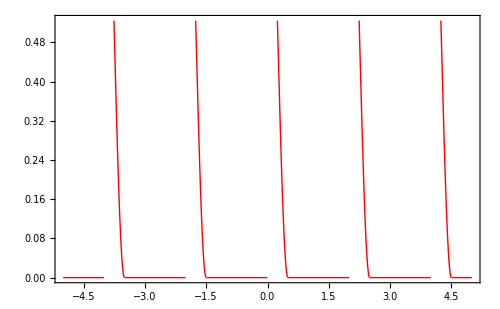

```mathematica
Plot[HannWindow[Abs[Mod[x,2]]],{x,-5,5}]
```

The separation between two first-order tones is

```mathematica
nm=10^-9;MHz=10^6;μs=10^-6;mm=10^-3;
rep={λ-> 1064 nm, ΔF->x MHz, v-> 4.26 mm/μs};
(λ ΔF)/v/.rep//ScientificForm
```

(2.49765×10^-4) x